```mathematica
EdgesInColor[edges_,color_]:=Map[#->Directive[color,Thick]&,edges]
```

```mathematica
EdgesInColor2[assoc_,edges_,color_]:=Block[{result=assoc},
Table[
If[KeyExistsQ[result,e],
result[e]=Join[result[e],color]
,
result[e]=color
]
,{e,edges}
];
result
]
```

```mathematica
BlurAssoc[assoc_]:=Block[{result=assoc},
Table[
result[k]={Thickness[0.015],If[Length[result[k]]==1,result[k],{Blend[result[k]]}]}
,{k,Keys[result]}
];
result]
```

```mathematica
AssocToRule[assoc_]:=Table[
k->assoc[k]
,{k,Keys[assoc]}
]
```

```mathematica
QuadrilateralsWithPattern[7,5]//Length
```

16

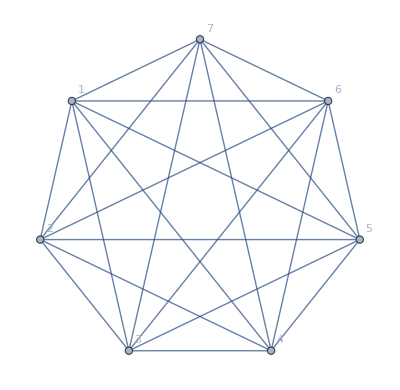
{{16,v1x246x35x7,-Graphics-13♁27♁46♁5
17♁24♁36♁5
17♁26♁35♁4
14♁27♁36♁5
17♁25♁36♁4
16
{27♁35♁46,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,14♁27♁36,14♁27♁35,14♁26♁35,14♁25♁36,13♁27♁46,13♁25♁46,13♁246}},{16,v1x247x35x6,-Graphics-13♁26♁47♁5
16♁24♁37♁5
16♁27♁35♁4
14♁26♁37♁5
16♁25♁37♁4
16
{26♁35♁47,247♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,14♁27♁35,14♁26♁37,14♁26♁35,14♁25♁37,13♁26♁47,13♁25♁47,13♁247}},{19,v16x24x35x7,-Graphics-13♁27♁46♁5
16♁24♁37♁5
16♁27♁35♁4
14♁27♁36♁5
16♁25♁37♁4
19
{27♁35♁46,25♁37♁46,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,146♁25,14♁25♁37,14♁25♁36,136♁27,13♁27♁46,136♁25,13♁25♁46,136♁24}},{19,v17x24x35x6,-Graphics-13♁27♁46♁5
17♁24♁36♁5
16♁27♁35♁4
14♁27♁36♁5
17♁25♁36♁4
19
{27♁35♁46,17♁35♁46,17♁25♁46,17♁25♁36,17♁24♁36,17♁24♁35,16♁27♁35,16♁24♁35,146♁35,146♁27,14♁27♁36,14♁27♁35,146♁25,14♁25♁36,136♁27,13♁27♁46,136♁25,13♁25♁46,136♁24}},{19,v17x24x35x6,-Graphics-13♁26♁47♁5
16♁24♁37♁5
17♁26♁35♁4
14♁26♁37♁5
16♁25♁37♁4
19
{26♁35♁47,17♁26♁35,17♁24♁35,16♁35♁47,16♁25♁47,16♁25♁37,16♁24♁37,16♁24♁35,147♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,137♁26,13♁26♁47,137♁25,13♁25♁47,137♁24}},{19,v17x24x35x6,-Graphics-13♁26♁47♁5
17♁24♁36♁5
17♁26♁35♁4
14♁26♁37♁5
17♁25♁36♁4
19
{26♁35♁47,25♁36♁47,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,147♁36,147♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,137♁26,13♁26♁47,137♁25,13♁25♁47,137♁24}},{19,v1x246x35x7,-Graphics-13♁27♁46♁5
16♁24♁37♁5
16♁27♁35♁4
14♁26♁37♁5
16♁25♁37♁4
19
{27♁35♁46,25♁37♁46,246♁37,246♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,13♁27♁46,13♁25♁46,13♁246}},{19,v1x247x35x6,-Graphics-13♁26♁47♁5
17♁24♁36♁5
17♁26♁35♁4
14♁27♁36♁5
17♁25♁36♁4
19
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁35,147♁25,14♁25♁36,13♁26♁47,13♁25♁47,13♁247}},{24,v1x246x35x7,-Graphics-13♁27♁46♁5
17♁24♁36♁5
17♁26♁35♁4
14♁26♁37♁5
17♁25♁36♁4
24
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,14♁25♁37,14♁25♁36,137♁46,13♁27♁46,137♁26,137♁25,13♁25♁46,137♁24,13♁246}},{24,v1x247x35x6,-Graphics-13♁26♁47♁5
16♁24♁37♁5
16♁27♁35♁4
14♁27♁36♁5
16♁25♁37♁4
24
{26♁35♁47,25♁36♁47,247♁36,247♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,14♁25♁37,14♁25♁36,136♁47,136♁27,13♁26♁47,136♁25,13♁25♁47,13♁247,136♁24}},{27,v17x24x35x6,-Graphics-13♁27♁46♁5
17♁24♁36♁5
16♁27♁35♁4
14♁27♁36♁5
16♁25♁37♁4
27
{27♁35♁46,25♁37♁46,17♁35♁46,17♁25♁46,17♁25♁36,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁25,136♁25,13♁25♁46,137♁24,136♁24}},{27,v17x24x35x6,-Graphics-13♁27♁46♁5
16♁24♁37♁5
16♁27♁35♁4
14♁27♁36♁5
17♁25♁36♁4
27
{27♁35♁46,25♁37♁46,17♁35♁46,17♁25♁46,17♁25♁36,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁25,136♁25,13♁25♁46,137♁24,136♁24}},{27,v17x24x35x6,-Graphics-13♁26♁47♁5
17♁24♁36♁5
17♁26♁35♁4
14♁26♁37♁5
16♁25♁37♁4
27
{26♁35♁47,25♁36♁47,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁25♁47,16♁25♁37,16♁24♁37,16♁24♁35,147♁36,147♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,137♁24,136♁24}},{27,v17x24x35x6,-Graphics-13♁26♁47♁5
16♁24♁37♁5
17♁26♁35♁4
14♁26♁37♁5
17♁25♁36♁4
27
{26♁35♁47,25♁36♁47,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁25♁47,16♁25♁37,16♁24♁37,16♁24♁35,147♁36,147♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,137♁24,136♁24}},{28,v1x246x35x7,-Graphics-13♁27♁46♁5
16♁24♁37♁5
17♁26♁35♁4
14♁26♁37♁5
16♁25♁37♁4
28
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁246,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,137♁46,13♁27♁46,137♁26,137♁25,13♁25♁46,137♁24,13♁246}},{28,v1x247x35x6,-Graphics-13♁26♁47♁5
17♁24♁36♁5
16♁27♁35♁4
14♁27♁36♁5
17♁25♁36♁4
28
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁247,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁35,147♁25,14♁25♁36,136♁47,136♁27,13♁26♁47,136♁25,13♁25♁47,13♁247,136♁24}},{35,v1x246x35x7,-Graphics-13♁27♁46♁5
17♁24♁36♁5
16♁27♁35♁4
14♁26♁37♁5
16♁25♁37♁4
35
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁26,137♁25,136♁25,13♁25♁46,137♁24,13♁246,136♁24}},{35,v1x246x35x7,-Graphics-13♁27♁46♁5
17♁24♁36♁5
16♁27♁35♁4
14♁26♁37♁5
17♁25♁36♁4
35
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁26,137♁25,136♁25,13♁25♁46,137♁24,13♁246,136♁24}},{35,v1x246x35x7,-Graphics-13♁27♁46♁5
16♁24♁37♁5
16♁27♁35♁4
14♁26♁37♁5
17♁25♁36♁4
35
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁26,137♁25,136♁25,13♁25♁46,137♁24,13♁246,136♁24}},{35,v1x246x35x7,-Graphics-13♁27♁46♁5
17♁24♁36♁5
17♁26♁35♁4
14♁26♁37♁5
16♁25♁37♁4
35
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁26,137♁25,136♁25,13♁25♁46,137♁24,13♁246,136♁24}},{35,v1x246x35x7,-Graphics-13♁27♁46♁5
16♁24♁37♁5
17♁26♁35♁4
14♁26♁37♁5
17♁25♁36♁4
35
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁26,137♁25,136♁25,13♁25♁46,137♁24,13♁246,136♁24}},{35,v1x246x35x7,-Graphics-13♁27♁46♁5
16♁24♁37♁5
17♁26♁35♁4
14♁27♁36♁5
16♁25♁37♁4
35
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁26,137♁25,136♁25,13♁25♁46,137♁24,13♁246,136♁24}},{35,v1x246x35x7,-Graphics-13♁27♁46♁5
17♁24♁36♁5
17♁26♁35♁4
14♁27♁36♁5
16♁25♁37♁4
35
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁26,137♁25,136♁25,13♁25♁46,137♁24,13♁246,136♁24}},{35,v1x246x35x7,-Graphics-13♁27♁46♁5
16♁24♁37♁5
17♁26♁35♁4
14♁27♁36♁5
17♁25♁36♁4
35
{27♁35♁46,25♁37♁46,246♁37,246♁35,17♁35♁46,17♁26♁35,17♁25♁46,17♁25♁36,17♁246,17♁24♁36,17♁24♁35,16♁27♁35,16♁25♁37,16♁24♁37,16♁24♁35,146♁37,146♁35,146♁27,14♁27♁36,14♁27♁35,14♁26♁37,14♁26♁35,146♁25,14♁25♁37,14♁25♁36,137♁46,136♁27,13♁27♁46,137♁26,137♁25,136♁25,13♁25♁46,137♁24,13♁246,136♁24}},{35,v1x247x35x6,-Graphics-13♁26♁47♁5
17♁24♁36♁5
16♁27♁35♁4
14♁26♁37♁5
16♁25♁37♁4
35
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,136♁27,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,13♁247,137♁24,136♁24}},{35,v1x247x35x6,-Graphics-13♁26♁47♁5
17♁24♁36♁5
16♁27♁35♁4
14♁26♁37♁5
17♁25♁36♁4
35
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,136♁27,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,13♁247,137♁24,136♁24}},{35,v1x247x35x6,-Graphics-13♁26♁47♁5
16♁24♁37♁5
16♁27♁35♁4
14♁26♁37♁5
17♁25♁36♁4
35
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,136♁27,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,13♁247,137♁24,136♁24}},{35,v1x247x35x6,-Graphics-13♁26♁47♁5
16♁24♁37♁5
17♁26♁35♁4
14♁27♁36♁5
16♁25♁37♁4
35
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,136♁27,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,13♁247,137♁24,136♁24}},{35,v1x247x35x6,-Graphics-13♁26♁47♁5
17♁24♁36♁5
17♁26♁35♁4
14♁27♁36♁5
16♁25♁37♁4
35
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,136♁27,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,13♁247,137♁24,136♁24}},{35,v1x247x35x6,-Graphics-13♁26♁47♁5
16♁24♁37♁5
17♁26♁35♁4
14♁27♁36♁5
17♁25♁36♁4
35
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,136♁27,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,13♁247,137♁24,136♁24}},{35,v1x247x35x6,-Graphics-13♁26♁47♁5
17♁24♁36♁5
16♁27♁35♁4
14♁27♁36♁5
16♁25♁37♁4
35
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,136♁27,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,13♁247,137♁24,136♁24}},{35,v1x247x35x6,-Graphics-13♁26♁47♁5
16♁24♁37♁5
16♁27♁35♁4
14♁27♁36♁5
17♁25♁36♁4
35
{26♁35♁47,25♁36♁47,247♁36,247♁35,17♁26♁35,17♁25♁36,17♁24♁36,17♁24♁35,16♁35♁47,16♁27♁35,16♁25♁47,16♁25♁37,16♁247,16♁24♁37,16♁24♁35,147♁36,147♁35,14♁27♁36,14♁27♁35,147♁26,14♁26♁37,14♁26♁35,147♁25,14♁25♁37,14♁25♁36,136♁47,136♁27,137♁26,13♁26♁47,137♁25,136♁25,13♁25♁47,13♁247,137♁24,136♁24}}}

```mathematica
With[
{nodes=7},
Monitor[
Sort[
Flatten[
Table[
Table[
Table[
Table[
Table[
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]],
colors=Association[]
},
colors=EdgesInColor2[colors,e1,{Yellow}];
colors=EdgesInColor2[colors,e2,{Red}];
colors=EdgesInColor2[colors,e3,{Darker[Green]}];
colors=EdgesInColor2[colors,e4,{Blue}];
colors=EdgesInColor2[colors,e5,{Orange}];
colors=BlurAssoc[colors];
Block[
{
gf=Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]], SymbolLevel[#]==4&],
first,
efirst
},
first=First[Select[gf,HasTrianglePattern[SymbolToSets[#]]&]];
efirst=EdgeList[GraphComplement[GraphFromSets[SymbolToSets[first]]]];
colors=EdgesInColor2[colors,efirst,{Thickness[0.08]}];
{Length[gf],
first,
Labeled[
CompleteGraph[nodes,
EdgeStyle->AssocToRule[colors],
VertexLabels->"Name",
ImageSize->400
],
Column[{Style[SetsToLabel[part1],Darker[Yellow]],Style[SetsToLabel[part2],Red],Style[SetsToLabel[part3],Darker[Green]],Style[SetsToLabel[part4],Blue],Style[SetsToLabel[part5],Orange],
Length[gf],
Map[With[{s=SymbolToSets[#]},Style[SetsToLabel2[s],If[HasQuadrilateralPattern[s],Blue,If[HasTrianglePattern[s],Red,Black]]]]&,gf]}]
]
}
]
],
{part5,Take[QuadrilateralsWithPattern[nodes,5],2]}
],
{part4,Take[QuadrilateralsWithPattern[nodes,4],2]}
],
{part3,Take[QuadrilateralsWithPattern[nodes,3],2]}
],
{part2,Take[QuadrilateralsWithPattern[nodes,2],2]}
],
{part1,Take[QuadrilateralsWithPattern[nodes,1],2]}
],4]
],
{part1,part2,part3,part4,part5}
]
]
```

```mathematica
{Thick}
```

{Thickness[Large]}